# Geometry Theorems: Lean 4 Proofs, Verified in Wolfram Language

## A computer-algebra companion to MyProject/Geometry.lean

This notebook mirrors, theorem by theorem, the six plane-geometry theorems that are formally proved in Lean 4 in MyProject/Geometry.lean of this project. Each section states the theorem, names the corresponding Lean theorem, and verifies it symbolically. Evaluate the whole notebook with Evaluation > Evaluate Notebook; every check should return True.

Important difference: Wolfram's Simplify is a computer-algebra check -- you trust the CAS implementation. Lean is a proof assistant: every step is verified by a small logical kernel, so a successful compile IS the proof. The math content, however, is exactly the same: points are integer (here: symbolic) coordinates, and each geometric statement is translated into an algebraic identity.

## Setup: points, vectors, dot product, squared distance

Same definitions as the Lean file. Note that A, B, C, D, N are reserved symbols in Wolfram Language, so points are named pA, pB, pC, pD and midpoints mM, mN.

```mathematica
vec[a_, b_] := b - a        (* vector from a to b *)
dot[u_, v_] := u . v         (* dot product *)
distSq[a_, b_] := (b - a) . (b - a)   (* squared distance *)
```

```mathematica
pA = {ax, ay}; pB = {bx, by}; pC = {cx, cy};  (* symbolic points *)
```

## Theorem 1: symmetry of distance (Lean: distSq_symm)

|AB|^2 = |BA|^2. In Lean this needs the expansion (a-b)^2 = (b-a)^2 plus commutativity rewrites; here Simplify does the algebra.

```mathematica
Simplify[distSq[pA, pB] == distSq[pB, pA]]
```

True

## Theorem 2: Pythagorean theorem (Lean: pythagoras)

If the angle at A is right (dot product of vectors AB and AC is zero) then |BC|^2 = |AB|^2 + |AC|^2. The key identity, proved as pythagoras_vec in Lean, is that |BC|^2 - |AB|^2 - |AC|^2 = -2 (AB . AC) identically. So the difference plus 2 (AB . AC) expands to exactly 0:

```mathematica
Expand[distSq[pB, pC] - distSq[pA, pB] - distSq[pA, pC] + 2 dot[vec[pA, pB], vec[pA, pC]]] === 0
```

Equivalently, assume the right angle and let Simplify use it:

```mathematica
Simplify[distSq[pB, pC] == distSq[pA, pB] + distSq[pA, pC], Assumptions -> dot[vec[pA, pB], vec[pA, pC]] == 0]
```

## Theorem 3: the 3-4-5 right triangle (Lean: pythagoras_3_4_5)

A concrete instance: O(0,0), A(3,0), B(0,4). In Lean the tactic `decide` just computes both sides; here the kernel evaluates them too.

```mathematica
distSq[{3, 0}, {0, 4}] == distSq[{0, 0}, {3, 0}] + distSq[{0, 0}, {0, 4}]
```

distSq[{3,0},{0,4}]==distSq[{0,0},{0,4}]+distSq[{0,0},{3,0}]

```mathematica
{distSq[{3, 0}, {0, 4}], distSq[{0, 0}, {3, 0}], distSq[{0, 0}, {0, 4}]}   (* 25 = 9 + 16 *)
```

{distSq[{3,0},{0,4}],distSq[{0,0},{3,0}],distSq[{0,0},{0,4}]}

## Theorem 4: triangle midsegment (Lean: midsegment)

mM and mN are the midpoints of AB and AC. The single vector equation 2 MN = BC encodes both conclusions of the midsegment theorem: MN is parallel to BC and half its length. (Lean states the midpoint condition as 2M = A + B to stay inside the integers; over the rationals we can just divide by 2.)

```mathematica
mM = (pA + pB)/2; mN = (pA + pC)/2;
Simplify[2 vec[mM, mN] == vec[pB, pC]]
```

vec[pB,pC]==2 vec[(pA+pB)/2,(pA+pC)/2]

## Theorem 5: parallelogram diagonals bisect each other (Lean: parallelogram_diag)

ABCD is a parallelogram when vector AB equals vector DC, i.e. pD = pC - vec(A,B). Then the midpoints of the two diagonals AC and BD coincide.

```mathematica
pD = pC - vec[pA, pB];
Simplify[(pA + pC)/2 == (pB + pD)/2]
```

pA+vec[pA,pB]==pB

## Theorem 6: centroid divides the median 2 : 1 (Lean: centroid_divides)

G = (A + B + C)/3 is the centroid and mBC the midpoint of BC. The vector equation AG = 2 GM says G lies on the median from A and divides it in ratio 2 : 1.

```mathematica
pG = (pA + pB + pC)/3; mBC = (pB + pC)/2;
Simplify[vec[pA, pG] == 2 vec[pG, mBC]]
```

vec[pA,1/3 (pA+pB+pC)]==2 vec[1/3 (pA+pB+pC),(pB+pC)/2]

## Picture: the 3-4-5 triangle and its midsegment

The red segment joins the midpoints of the two legs; by Theorem 4 it is parallel to the hypotenuse and half as long.

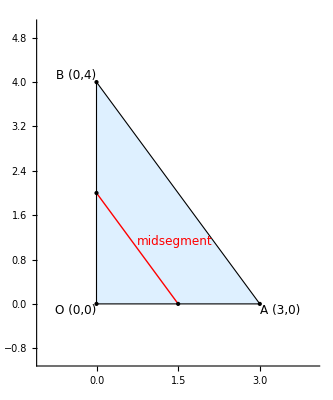

```mathematica
Graphics[{
  EdgeForm[{Thick, Black}], FaceForm[LightBlue],
  Polygon[{{0, 0}, {3, 0}, {0, 4}}],
  Red, Thick, Line[{{3/2, 0}, {0, 2}}],
  Black, PointSize[Large],
  Point[{{0, 0}, {3, 0}, {0, 4}, {3/2, 0}, {0, 2}}],
  Text[Style["O (0,0)", 12], {0, 0}, {1.3, 1.3}],
  Text[Style["A (3,0)", 12], {3, 0}, {-1.2, 1.3}],
  Text[Style["B (0,4)", 12], {0, 4}, {1.2, -1.3}],
  Text[Style["midsegment", 12, Red], {3/4, 1}, {-1.2, -1}]
}, Axes -> True, PlotRange -> {{-1, 4}, {-1, 5}}]
```

## Where to go next

The Lean file proves the same statements with machine-checked rigor using only core tactics (simp, rw, omega, decide). To see it, open MyProject/Geometry.lean and run `lake build` -- a successful build means the Lean kernel accepted every proof. Try changing a conclusion (e.g. the 2:1 ratio to 3:1) and watch Lean reject it, then try the same experiment here with Simplify returning False instead of True.